```mathematica
Integrate[Sign[t-ArcTan[-a,√(1-a^2)]]Sign[t-2Pi+ArcTan[-a,√(1-a^2)]]Sqrt[1-Sin[t]^2/(1+a^2+2a Cos[t])]/(1+a^2+2a Cos[t]),{t,0,Pi}]
```

$Aborted

```mathematica
Integrate[]
```

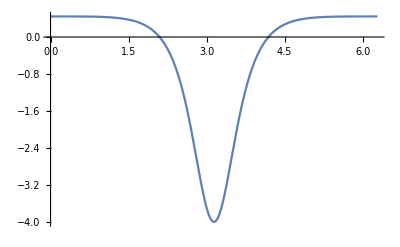

```mathematica
Plot[Sign[t-ArcTan[-a,√(1-a^2)]]Sign[t-2Pi+ArcTan[-a,√(1-a^2)]]Sqrt[1-Sin[t]^2/(1+a^2+2a Cos[t])]/(1+a^2+2a Cos[t])/.a->.5,{t,0,2Pi}]
```

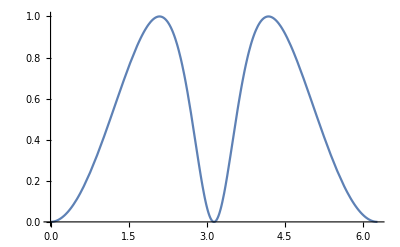

```mathematica
Plot[Sin[t]^2/(1+a^2+2a Cos[t])/.a->.5,{t,0,2Pi}]
```

```mathematica
D[Sin[t]^2/(1+a^2+2a Cos[t]),t]
```

(2 Cos[t] Sin[t])/(1+a^2+2 a Cos[t])+(2 a Sin[t]^3)/((1+a^2+2 a Cos[t])^2)

```mathematica
Solve[%==0,t]
```

{{t→ConditionalExpression[2 π C[1],C[1]∈ℤ]},{t→ConditionalExpression[π+2 π C[1],C[1]∈ℤ]},{t→ConditionalExpression[ArcTan[-1/a,-(√(-1+a^2))/a]+2 π C[1],C[1]∈ℤ]},{t→ConditionalExpression[ArcTan[-1/a,(√(-1+a^2))/a]+2 π C[1],C[1]∈ℤ]},{t→ConditionalExpression[ArcTan[-a,-√(1-a^2)]+2 π C[1],C[1]∈ℤ]},{t→ConditionalExpression[ArcTan[-a,√(1-a^2)]+2 π C[1],C[1]∈ℤ]}}

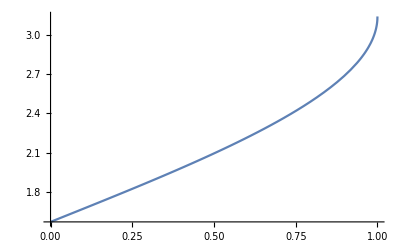

```mathematica
Plot[ArcTan[-a,√(1-a^2)],{a,0,1}]
```

```mathematica
Integrate[1/Sqrt[1+a^2+2a Cos[t]],{t,0,2Pi}]
```

ConditionalExpression[(2 EllipticK[-(4 a)/(-1+a)^2])/(√((-1+a)^2))+(2 EllipticK[(4 a)/(1+a)^2])/(√((1+a)^2)),(Re[1/a+a]≥2||Re[1/a+a]≤-2||1/a+a∉ℝ)&&Re[(-2+a) a]>-1&&Re[a (2+a)]>-1]

```mathematica
FullSimplify[(2 EllipticK[-(4 a)/(-1+a)^2])/(√((-1+a)^2))+(2 EllipticK[(4 a)/(1+a)^2])/(√((1+a)^2))]
```

-(2 EllipticK[-(4 a)/(-1+a)^2])/(-1+a)+(2 EllipticK[(4 a)/(1+a)^2])/(1+a)

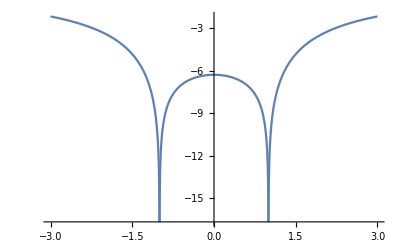

```mathematica
Plot[-((2 EllipticK[-(4 a)/(-1+a)^2])/(√((-1+a)^2))+(2 EllipticK[(4 a)/(1+a)^2])/(√((1+a)^2))),{a,-3,3}]
```

```mathematica
$Assumptions=True
```

True

```mathematica
D[(2 EllipticK[-(4 a)/(-1+a)^2])/(√((-1+a)^2))+(2 EllipticK[(4 a)/(1+a)^2])/(√((1+a)^2)),a]//FullSimplify
```

(-(-1+a)^2 √((1+a)^2) EllipticE[-(4 a)/(-1+a)^2]-(1+a) (√((-1+a)^2) (1+a) EllipticE[(4 a)/(1+a)^2]+(-1+a) (√((1+a)^2) EllipticK[-(4 a)/(-1+a)^2]+√((-1+a)^2) EllipticK[(4 a)/(1+a)^2])))/(√((-1+a)^2) a √((1+a)^2) (-1+a^2))

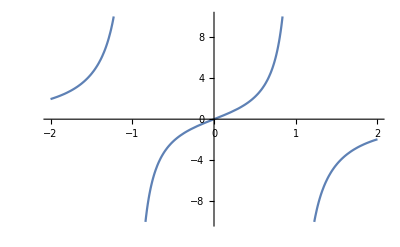

```mathematica
Plot[(-(-1+a)^2 √((1+a)^2) EllipticE[-(4 a)/(-1+a)^2]-(1+a) (√((-1+a)^2) (1+a) EllipticE[(4 a)/(1+a)^2]+(-1+a) (√((1+a)^2) EllipticK[-(4 a)/(-1+a)^2]+√((-1+a)^2) EllipticK[(4 a)/(1+a)^2])))/(√((-1+a)^2) a √((1+a)^2) (-1+a^2)),{a,-2,2},PlotRange->{-10,10}]
```